```mathematica
u[w_,θ_,UH_]:=√((-UH+w Cos[θ])^2+w^2 Sin[θ]^2);
sig[x_]:=(1.0-(0.102046)*Log[(x)])^2;
wc=200;
h[w_,θ_,UH_]:=u[w,θ,UH]*sig[u[w,θ,UH]]/((w+wc)*sig[(w+wc)]);
```

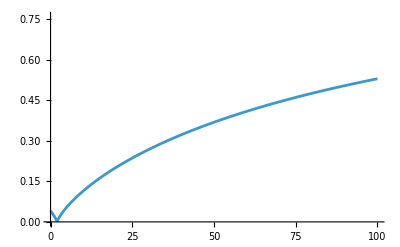

```mathematica
Plot[h[w,0*π/180, 2.0],{w,0,100},PlotRange->{{0,100},{0,0.76}}]
```